Variables

```mathematica
g=9.81;
l = 5;
poc=1;
time = {t, 0, 25};
init = {y[0] == poc, y'[0] == 0};
rovnice = y''[t] + g/l *Sin[y[t]] == 0;
```

--------------------------------------------------------------------------------------------------------------------Ukol(1)--------------------------------------------------------------------------------------------------------------------

```mathematica
Series[1/(1-x)^(1/2),{x,0,10}]
```

1+x/2+(3 x^2)/8+(5 x^3)/16+(35 x^4)/128+(63 x^5)/256+(231 x^6)/1024+(429 x^7)/2048+(6435 x^8)/32768+(12155 x^9)/65536+(46189 x^10)/262144+O[x]^11

```mathematica
k = θ/2;
```

```mathematica
f[x_]:=1+x/2+(3 x^2)/8;
ff[x_] := f[x^2]
```

```mathematica
ff[k*Sin[ϕ]]
```

1+1/8 θ^2 Sin[ϕ]^2+3/128 θ^4 Sin[ϕ]^4

```mathematica
Integrate[ff[k*Sin[ϕ]],{ϕ,0,Pi/2}]
```

(π (1024+64 θ^2+9 θ^4))/2048

```mathematica
Perioda[θ_] := (π (1024+64 θ^2+9 θ^4))/2048*4*Sqrt[l/g]
```

```mathematica
2 π ((9 θ^4)/1024+θ^2/16+1) √(l/g)// TeXForm
```

4.4857 \left(\frac{9 \theta ^4}{1024}+\frac{\theta ^2}{16}+1\right)

--------------------------------------------------------------------------------------------------------------------(0-primou integraci)--------------------------------------------------------------------------------------------------------------------

```mathematica
Elip[θ_]:=Integrate[4*Sqrt[l/g]*1/Sqrt[1-Sin[θ/2]^2*Sin[y]^2],{y,0,Pi/2}]
```

--------------------------------------------------------------------------------------------------------------------Ukol(2)--------------------------------------------------------------------------------------------------------------------

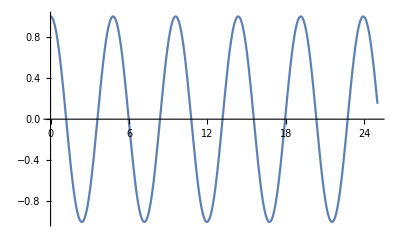

```mathematica
list={};
sol:=NDSolve[{rovnice, init, WhenEvent[y[t] == 0, AppendTo[list,t]]}, y, time]
Plot[Evaluate[y[t] /. sol], time]
```

Porovnani:

```mathematica
Grid[{{"MathematicaDSolve","AproxPeriod","ElipIntegruj","SymplecticPartitionedRungeKutta","ProjectionExplicitRungeKutta","PokazEuler"},{First[list]*4,Perioda[poc],N[Elip[poc]],First[pruchod]*4,First[list3]*4,First[listEU]*4}},Frame->All]
```

MathematicaDSolve | AproxPeriod | ElipIntegruj | SymplecticPartitionedRungeKutta | ProjectionExplicitRungeKutta | PokazEuler
4.78326 | 4.80548 | 4.78326 | 4.7827 | 4.78326 | 4.80032

--------------------------------------------------------------------------------------------------------------------Ukol(3)--------------------------------------------------------------------------------------------------------------------

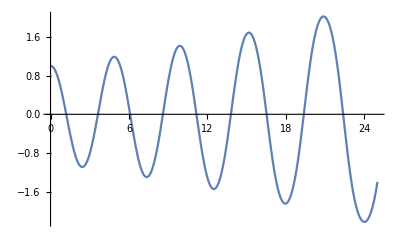

```mathematica
listEU={};
sol2:=NDSolve[{rovnice, init, WhenEvent[y[t] == 0, AppendTo[listEU,t]]}, y, time,Method->"ExplicitEuler",StartingStepSize->1/25,MaxStepSize->0.1]
Plot[Evaluate[y[t]  /. sol2], time]
```

--------------------------------------------------------------------------------------------------------------------Ukol(4)--------------------------------------------------------------------------------------------------------------------

```mathematica
energie=1/2 *(y'[t])^2-g/l *Cos[y[t]];
energie0=-g/l *Cos[poc]
```

-1.06007

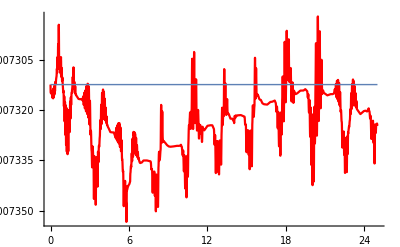

```mathematica
p1=Plot[Evaluate[energie/. sol], time,PlotStyle->Red] ;
p2 = Plot[energie0,time, PlotStyle->Thick];
Show[p1,p2,PlotRange->All]
```

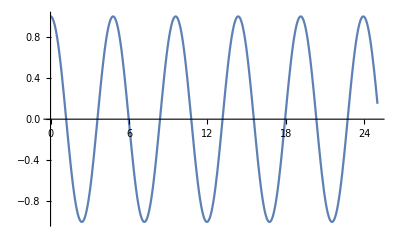

```mathematica
list3={};
sol3I:=NDSolve[{rovnice, init, WhenEvent[y[t] == 0, AppendTo[list3,t]]}, y, time, Method->{"Projection",Method->"ExplicitRungeKutta","Invariants"->energie0}]
Plot[Evaluate[y[t] /. sol3I], time]
```

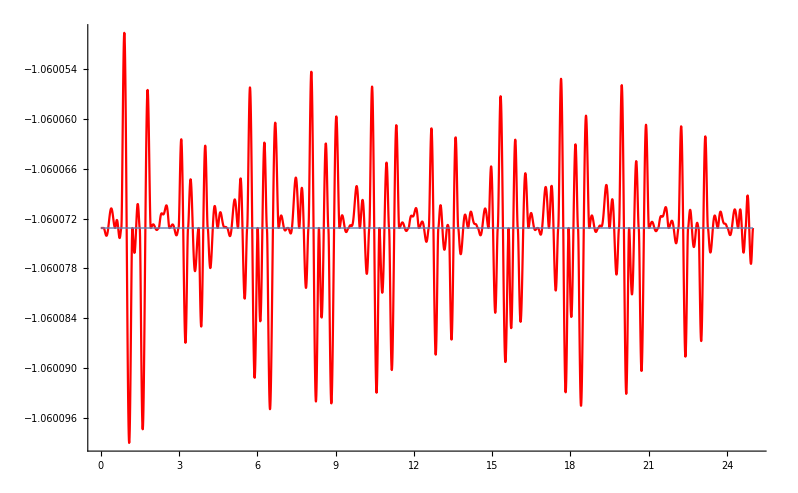

```mathematica
p1=Plot[Evaluate[energie/. sol3I], time,PlotStyle->Red] ;
p2 = Plot[energie0,time, PlotStyle->Thick];
Show[p1,p2,PlotRange->All]
```

--------------------------------------------------------------------------------------------------------------------SympleticPartionedRungeKutta--------------------------------------------------------------------------------------------------------------------
ve druhem 2pendulum.nb

```mathematica
H = p[t]^2/2 -g/l *Cos[q[t]];
eqs = {p'[t] == -D[H, q[t]], q'[t] == D[H, p[t]]};
ics = {p[0] == 0,q[0] == poc};
vars = {q[t], p[t]};
step = 1/25;
pruchod = {};
```

```mathematica
rese=NDSolve[{eqs,ics, WhenEvent[q[t] == 0, AppendTo[pruchod,t]]},vars,time,Method->{"SymplecticPartitionedRungeKutta","DifferenceOrder"->2,"PositionVariables"->{q[t]}},StartingStepSize->step, MaxSteps->Infinity];
```

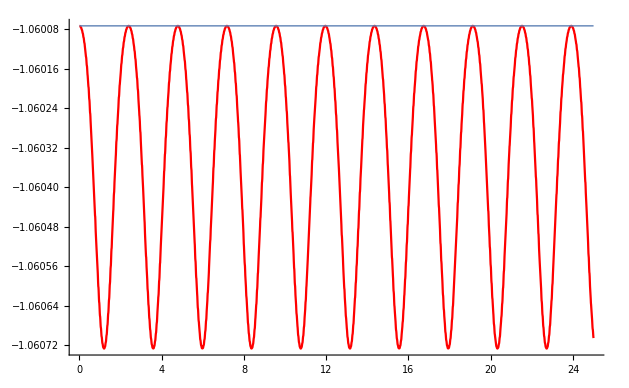

```mathematica
p1=Plot[Evaluate[p[t]^2/2 -g/l *Cos[q[t]]/.rese], time,PlotStyle->Red] ;
p2 = Plot[-g/l *Cos[poc],time, PlotStyle->Thick];
Show[p1,p2,PlotRange->All]
```

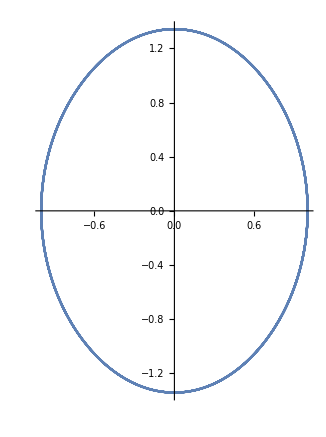

```mathematica
ParametricPlot[Evaluate[vars/. rese],Evaluate[time]]
```

```mathematica
reseeu=NDSolve[{eqs,ics},vars,time,Method->"ExplicitEuler",StartingStepSize->step,MaxSteps->Infinity];
```

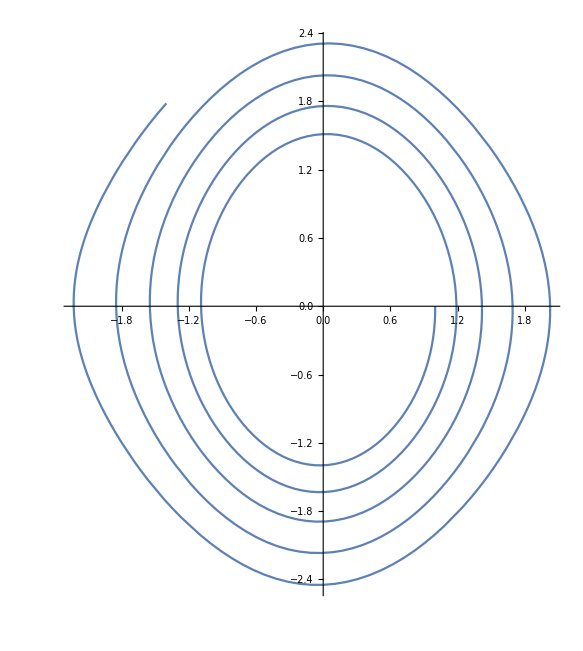

```mathematica
ParametricPlot[Evaluate[vars/. reseeu],Evaluate[time],PlotPoints->10]
```

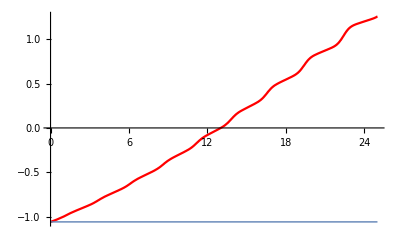

```mathematica
p1=Plot[Evaluate[p[t]^2/2 -g/l *Cos[q[t]]/. reseeu], time,PlotStyle->Red] ;
p2 = Plot[-g/l *Cos[poc],time, PlotStyle->Thick];
Show[p1,p2,PlotRange->All]
```

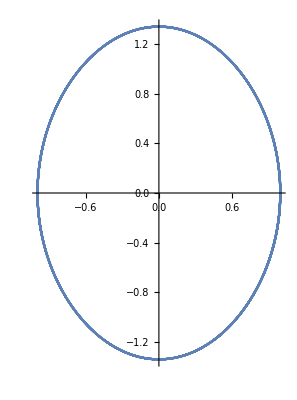

```mathematica
sol3E:=NDSolve[{y''[t] + g/l *Sin[y[t]] == 0, y[0] == poc, y'[0] == 0}, y, time,Method->{"Projection",Method->"ExplicitRungeKutta","Invariants"->-g/l *Cos[poc]},StartingStepSize->step,MaxSteps->Infinity]
ParametricPlot[Evaluate[{y[t], y'[t]}/. sol3E],Evaluate[time]]
```

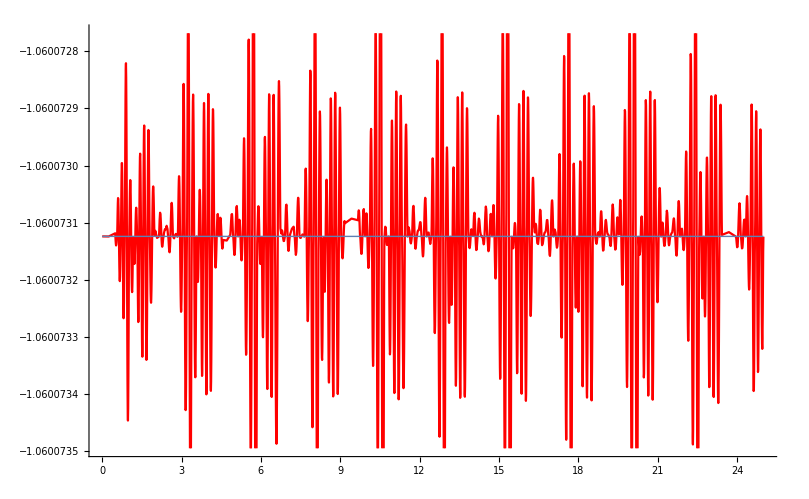

```mathematica
p1=Plot[Evaluate[1/2 *(y'[t])^2-g/l *Cos[y[t]]/. sol3E], time,PlotStyle->Red] ;
p2 = Plot[-g/l *Cos[poc],time, PlotStyle->Thick];
Show[p1,p2,PlotRange->All]
```

--------------------------------------------------------------------------------------------------------------------Ukol(5+6)--------------------------------------------------------------------------------------------------------------------

```mathematica
ϕ[t_]:=ϵ*A[t]+ϵ^3*B[t]+ϵ^5*C[t];
ω^2=O^2+ϵ^2*α+ϵ^4*β+ϵ^6*γ;
```

Set::write: Tag Power in ω^2 is Protected.

```mathematica
Series[Sin[x],{x,0,5}]
```

x-x^3/6+x^5/120+O[x]^6

```mathematica
roz =(ϵ*A''[t]+ϵ^3*B''[t]+ϵ^5*C̈́''[t])+(ω^2-ϵ^2*α-ϵ^4*β-ϵ^6*γ)*(ϵ*A[t]+ϵ^3*B[t]+ϵ^5*C[t]-((ϵ*A[t]+ϵ^3*B[t]+ϵ^5*C[t])^3)/6+((ϵ*A[t]+ϵ^3*B[t]+ϵ^5*C[t])^5)/120);
```

```mathematica
Collect[roz,ϵ]
```

-1/120 γ ϵ^31 C[t]^5+ϵ^7 (-γ A[t]+1/6 β A[t]^3-1/120 α A[t]^5-β B[t]+1/2 α A[t]^2 B[t]+1/24 ω^2 A[t]^4 B[t]-1/2 ω^2 A[t] B[t]^2-α C[t]-1/2 ω^2 A[t]^2 C[t])+ϵ^9 (1/6 γ A[t]^3-1/120 β A[t]^5-γ B[t]+1/2 β A[t]^2 B[t]-1/24 α A[t]^4 B[t]+1/2 α A[t] B[t]^2+1/12 ω^2 A[t]^3 B[t]^2-1/6 ω^2 B[t]^3-β C[t]+1/2 α A[t]^2 C[t]+1/24 ω^2 A[t]^4 C[t]-ω^2 A[t] B[t] C[t])+ϵ^11 (-1/120 γ A[t]^5+1/2 γ A[t]^2 B[t]-1/24 β A[t]^4 B[t]+1/2 β A[t] B[t]^2-1/12 α A[t]^3 B[t]^2+1/6 α B[t]^3+1/12 ω^2 A[t]^2 B[t]^3-γ C[t]+1/2 β A[t]^2 C[t]-1/24 α A[t]^4 C[t]+α A[t] B[t] C[t]+1/6 ω^2 A[t]^3 B[t] C[t]-1/2 ω^2 B[t]^2 C[t]-1/2 ω^2 A[t] C[t]^2)+ϵ^13 (-1/24 γ A[t]^4 B[t]+1/2 γ A[t] B[t]^2-1/12 β A[t]^3 B[t]^2+1/6 β B[t]^3-1/12 α A[t]^2 B[t]^3+1/24 ω^2 A[t] B[t]^4+1/2 γ A[t]^2 C[t]-1/24 β A[t]^4 C[t]+β A[t] B[t] C[t]-1/6 α A[t]^3 B[t] C[t]+1/2 α B[t]^2 C[t]+1/4 ω^2 A[t]^2 B[t]^2 C[t]+1/2 α A[t] C[t]^2+1/12 ω^2 A[t]^3 C[t]^2-1/2 ω^2 B[t] C[t]^2)+ϵ^15 (-1/12 γ A[t]^3 B[t]^2+1/6 γ B[t]^3-1/12 β A[t]^2 B[t]^3-1/24 α A[t] B[t]^4+1/120 ω^2 B[t]^5-1/24 γ A[t]^4 C[t]+γ A[t] B[t] C[t]-1/6 β A[t]^3 B[t] C[t]+1/2 β B[t]^2 C[t]-1/4 α A[t]^2 B[t]^2 C[t]+1/6 ω^2 A[t] B[t]^3 C[t]+1/2 β A[t] C[t]^2-1/12 α A[t]^3 C[t]^2+1/2 α B[t] C[t]^2+1/4 ω^2 A[t]^2 B[t] C[t]^2-(ω^2 C[t]^3)/6)+ϵ^17 (-1/12 γ A[t]^2 B[t]^3-1/24 β A[t] B[t]^4-1/120 α B[t]^5-1/6 γ A[t]^3 B[t] C[t]+1/2 γ B[t]^2 C[t]-1/4 β A[t]^2 B[t]^2 C[t]-1/6 α A[t] B[t]^3 C[t]+1/24 ω^2 B[t]^4 C[t]+1/2 γ A[t] C[t]^2-1/12 β A[t]^3 C[t]^2+1/2 β B[t] C[t]^2-1/4 α A[t]^2 B[t] C[t]^2+1/4 ω^2 A[t] B[t]^2 C[t]^2+(α C[t]^3)/6+1/12 ω^2 A[t]^2 C[t]^3)+ϵ^19 (-1/24 γ A[t] B[t]^4-1/120 β B[t]^5-1/4 γ A[t]^2 B[t]^2 C[t]-1/6 β A[t] B[t]^3 C[t]-1/24 α B[t]^4 C[t]-1/12 γ A[t]^3 C[t]^2+1/2 γ B[t] C[t]^2-1/4 β A[t]^2 B[t] C[t]^2-1/4 α A[t] B[t]^2 C[t]^2+1/12 ω^2 B[t]^3 C[t]^2+(β C[t]^3)/6-1/12 α A[t]^2 C[t]^3+1/6 ω^2 A[t] B[t] C[t]^3)+ϵ^21 (-1/120 γ B[t]^5-1/6 γ A[t] B[t]^3 C[t]-1/24 β B[t]^4 C[t]-1/4 γ A[t]^2 B[t] C[t]^2-1/4 β A[t] B[t]^2 C[t]^2-1/12 α B[t]^3 C[t]^2+(γ C[t]^3)/6-1/12 β A[t]^2 C[t]^3-1/6 α A[t] B[t] C[t]^3+1/12 ω^2 B[t]^2 C[t]^3+1/24 ω^2 A[t] C[t]^4)+ϵ^23 (-1/24 γ B[t]^4 C[t]-1/4 γ A[t] B[t]^2 C[t]^2-1/12 β B[t]^3 C[t]^2-1/12 γ A[t]^2 C[t]^3-1/6 β A[t] B[t] C[t]^3-1/12 α B[t]^2 C[t]^3-1/24 α A[t] C[t]^4+1/24 ω^2 B[t] C[t]^4)+ϵ^27 (-1/12 γ B[t]^2 C[t]^3-1/24 γ A[t] C[t]^4-1/24 β B[t] C[t]^4-(α C[t]^5)/120)+ϵ^29 (-1/24 γ B[t] C[t]^4-(β C[t]^5)/120)+ϵ^25 (-1/12 γ B[t]^3 C[t]^2-1/6 γ A[t] B[t] C[t]^3-1/12 β B[t]^2 C[t]^3-1/24 β A[t] C[t]^4-1/24 α B[t] C[t]^4+(ω^2 C[t]^5)/120)+ϵ (ω^2 A[t]+A''[t])+ϵ^3 (-α A[t]-1/6 ω^2 A[t]^3+ω^2 B[t]+B''[t])+ϵ^5 (-β A[t]+1/6 α A[t]^3+1/120 ω^2 A[t]^5-α B[t]-1/2 ω^2 A[t]^2 B[t]+ω^2 C[t]+C̈́''[t])

eps1:  ω^2 A[t]+A''[t]=0
eps3: -α A[t]-1/6 ω^2 A[t]^3+ω^2 B[t]+B''[t]=0
eps5: -β A[t]+1/6 α A[t]^3+1/120 ω^2 A[t]^5-α B[t]-1/2 ω^2 A[t]^2 B[t]+ω^2 C[t]+C̈́''[t]=0

```mathematica
A[t]=poc*Cos[ω*t];
B[t]=poc^3/192*(Cos[3*ω*t]-Cos[ω*t]);
α =-(ω^2*poc^2)/8;
```

```mathematica
-β A[t]+1/6 α A[t]^3+1/120 ω^2 A[t]^5-α B[t]-1/2 ω^2 A[t]^2 B[t]+ω^2 C[t]+C̈́''[t]
```

ω^2 C[t]-poc β Cos[t ω]-1/48 poc^5 ω^2 Cos[t ω]^3+1/120 poc^5 ω^2 Cos[t ω]^5+(poc^5 ω^2 (-Cos[t ω]+Cos[3 t ω]))/1536-1/384 poc^5 ω^2 Cos[t ω]^2 (-Cos[t ω]+Cos[3 t ω])+C̈́''[t]

```mathematica
-(-poc β Cos[t ω]-1/48 poc^5 ω^2 Cos[t ω]^3+1/120 poc^5 ω^2 Cos[t ω]^5+(poc^5 ω^2 (-Cos[t ω]+Cos[3 t ω]))/1536-1/384 poc^5 ω^2 Cos[t ω]^2 (-Cos[t ω]+Cos[3 t ω]))
```

poc β Cos[t ω]+1/48 poc^5 ω^2 Cos[t ω]^3-1/120 poc^5 ω^2 Cos[t ω]^5-(poc^5 ω^2 (-Cos[t ω]+Cos[3 t ω]))/1536+1/384 poc^5 ω^2 Cos[t ω]^2 (-Cos[t ω]+Cos[3 t ω])

C -> y

```mathematica
y''[t]+ω^2 *y[t]==poc β Cos[t ω]+1/48 poc^5 ω^2 Cos[t ω]^3-1/120 poc^5 ω^2 Cos[t ω]^5-(poc^5 ω^2 (-Cos[t ω]+Cos[3 t ω]))/1536+1/384 poc^5 ω^2 Cos[t ω]^2 (-Cos[t ω]+Cos[3 t ω])//TrigReduce
```

ω^2 y[t]+y''[t]==(7680 poc β Cos[t ω]+75 poc^5 ω^2 Cos[t ω]+20 poc^5 ω^2 Cos[3 t ω]+poc^5 ω^2 Cos[5 t ω])/7680

```mathematica
Solve[7680 poc β +75 poc^5 ω^2  ==0,β]
```

{{β→-5/512 poc^4 ω^2}}

```mathematica
β=-5/512 poc^4 ω^2;
```

```mathematica
rovniccce = ω^2 y[t]+y''[t]==(20 poc^5 ω^2 Cos[3 t ω]+poc^5 ω^2 Cos[5 t ω])/7680;
```

```mathematica
DSolve[{rovniccce,y[0]==0,y'[0]==0},y[t],t] //Simplify
```

{{y[t]→(poc^5 (62 Cos[t ω]+Cos[3 t ω]) Sin[t ω]^2)/46080}}

```mathematica
Solve[ω^2==g/l-(ω^2*poc^2)/8-5/512 poc^4 ω^2,ω]
```

{{ω→-1.31491},{ω→1.31491}}

```mathematica
M=1.311903939874637
```

1.3119

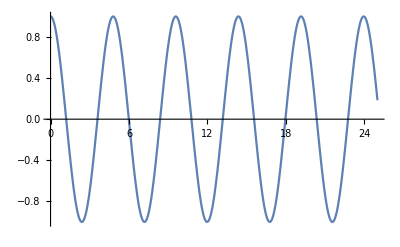

```mathematica
aproximace[t_] := poc*Cos[M*t]+poc^3/192*(Cos[3*M*t]-Cos[M*t])+(poc^5 (62 Cos[t M]+Cos[3 t M]) Sin[t M]^2)/46080;
Plot[aproximace[t], time]
```

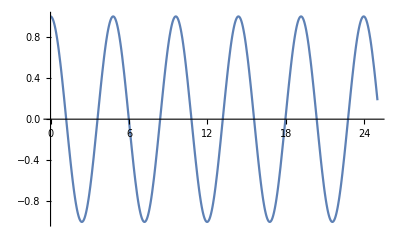

```mathematica
aprox[t_] := poc*Cos[M*t]+poc^3/192*(Cos[3*M*t]-Cos[M*t]);
Plot[aprox[t], time]
```

```mathematica
sl1=Table[aprox[t],{t, 0, 25,1}]
```

{1.,0.251026,-0.864483,-0.693485,0.502175,0.96057,-0.0170779,-0.969836,-0.472032,0.718202,0.84624,-0.284042,-0.999366,-0.21774,0.881673,0.66796,-0.531757,-0.950101,0.0512155,0.977883,0.441366,-0.742078,-0.826972,0.316752,0.997466,0.184221}

```mathematica
sl2 =Table[aproximace[t],{t, 0, 25,1}]
```

{1.,0.251334,-0.864769,-0.693957,0.502666,0.960668,-0.0171002,-0.969911,-0.472512,0.718658,0.846555,-0.284384,-0.999368,-0.218011,0.881931,0.668445,-0.532256,-0.950223,0.0512823,0.977939,0.441831,-0.742515,-0.827314,0.317124,0.997473,0.184453}

```mathematica
sl3=Table[Evaluate[y[t] /. sol], {t, 0, 25, 1}]
```

{{1.},{0.25972},{-0.875165},{-0.705212},{0.524199},{0.961383},{-0.0281047},{-0.974821},{-0.476062},{0.743075},{0.847561},{-0.313376},{-0.998554},{-0.20518},{0.900131},{0.665121},{-0.570615},{-0.945127},{0.0842176},{0.985415},{0.426352},{-0.778614},{-0.817381},{0.365974},{0.994218},{0.149941}}

```mathematica
Grid[{{"aprox","aproximace","NDSole"},{TableForm[sl1],TableForm[sl2],TableForm[sl3]}},Frame->All]
```

aprox | aproximace | NDSole
1.
0.251026
-0.864483
-0.693485
0.502175
0.96057
-0.0170779
-0.969836
-0.472032
0.718202
0.84624
-0.284042
-0.999366
-0.21774
0.881673
0.66796
-0.531757
-0.950101
0.0512155
0.977883
0.441366
-0.742078
-0.826972
0.316752
0.997466
0.184221 | 1.
0.251334
-0.864769
-0.693957
0.502666
0.960668
-0.0171002
-0.969911
-0.472512
0.718658
0.846555
-0.284384
-0.999368
-0.218011
0.881931
0.668445
-0.532256
-0.950223
0.0512823
0.977939
0.441831
-0.742515
-0.827314
0.317124
0.997473
0.184453 | 1.
0.25972
-0.875165
-0.705212
0.524199
0.961383
-0.0281047
-0.974821
-0.476062
0.743075
0.847561
-0.313376
-0.998554
-0.20518
0.900131
0.665121
-0.570615
-0.945127
0.0842176
0.985415
0.426352
-0.778614
-0.817381
0.365974
0.994218
0.149941